# Muon Production in SM - γ-> μ^- μ^+

## Load FeynArts and FormCalc

```mathematica
Quit[]
```

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts/FeynArts.m"
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
<<"/home/riccardo/Programs/FormCalc/FormCalc/FormCalc.m"
```

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

## Set-up

```mathematica
CKM=IndexDelta;
```

```mathematica
process={V[10]} -> {F[2,{2}], -F[2,{2}]};
```

```mathematica
name="A-mm-SMbgf";
```

```mathematica
SetOptions[InsertFields,Model->"SMbgf",GenericModel->"Lorentzbgf",InsertionLevel->Particles];
SetOptions[Paint,PaintLevel->{Classes},ColumnsXRows->{2,2}];
```

## Tree-Level

## Topologies

> Top. 1 ad/bdcd/0.m, 0 diagrams

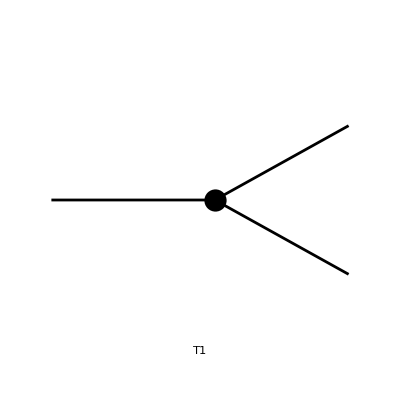

```mathematica
topsBorn=CreateTopologies[0,1->2,Adjacencies->3];
Paint[topsBorn];
```

## Insertions

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/FeynArts/FeynArts/Models/SMbgf.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 691 vertices

> 334 counterterms of order 1

> 2 counterterms of order 2

classes model {SMbgf} initialized

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 1 Generic, 1 Classes, 1 Particles insertions

in total: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 1 ad/bdcd/0.m, 0 diagrams

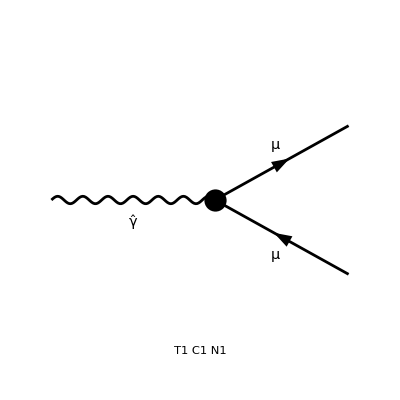

```mathematica
insBorn=InsertFields[topsBorn, process];
Paint[insBorn];
```

## Feynman Amplitudes

```mathematica
ClearProcess[]
```

```mathematica
ampBorn=CalcFeynAmp[CreateFeynAmp[insBorn,AmplitudeLevel->{Particles}],FermionChains -> Chiral]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

Amp[{{V[10],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-EL Mat[F1]-EL Mat[F2]]

## Squared Matrix Element

```mathematica
_Hel=0;
```

```mathematica
smBorn=SquaredME[ampBorn]//Simplify;
smBorn=smBorn/.HelicityME[smBorn];
smBorn=PolarizationSum[smBorn]//Simplify
```

> 4 helicity matrix elements

preparing FORM code in /home/riccardo/fc-hel-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-pol-1.frm

running FORM...

ok

8 Alfa MM2 π

## One-Loop

## Topologies

> Top. 1 ad/becf/dedfef.m, 0 diagrams

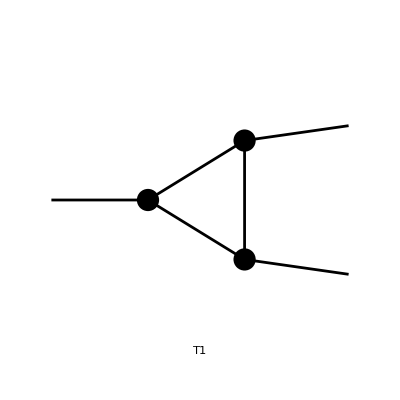

```mathematica
tops1Loop=CreateTopologies[1,1->2,Adjacencies->3,ExcludeTopologies->Reducible];
Paint[tops1Loop];
```

## Insertions

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 4 Generic, 6 Classes, 6 Particles insertions

in total: 4 Generic, 6 Classes, 6 Particles insertions

> Top. 1 ad/becf/dedfef.m, 0 diagrams

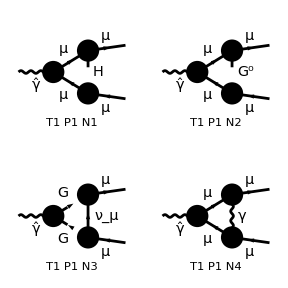

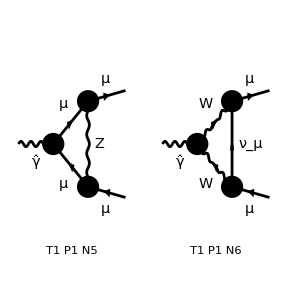

```mathematica
ins1Loop=InsertFields[tops1Loop, process];
Paint[ins1Loop, PaintLevel->{Particles}];
```

## Feynman Amplitudes

```mathematica
ClearProcess[]
```

```mathematica
amp1Loop=CalcFeynAmp[CreateFeynAmp[ins1Loop,AmplitudeLevel->{Particles}],FermionChains -> Chiral];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 6 Particles amplitudes

in total: 6 Particles amplitudes

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

## Squared Matrix Elements

```mathematica
_Hel=0;
```

```mathematica
sm1Loop=SquaredME[amp1Loop,ampBorn]//Simplify;
sm1Loop=sm1Loop/.HelicityME[sm1Loop];
sm1Loop=PolarizationSum[sm1Loop]//Simplify
```

> 16 helicity matrix elements

preparing FORM code in /home/riccardo/fc-hel-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-pol-1.frm

running FORM...

ok

-1/4 Alfa2 MM2 (-Sub15+Sub25+2 MM2 (Sub33+Sub39))

```mathematica
uv=UVDivergentPart[sm1Loop//.Subexpr[]]//Simplify
```

(Alfa2 Divergence MM2 (3 CW2 MM2+MW2+2 CW2 MW2-4 MW2 SW2+8 CW2 MW2 SW2+8 MW2 SW2^2))/(4 CW2 MW2 SW2)

## Amplitude manipulations

## Amplitude manipulation tools

```mathematica
selectFeynAmp[amp_,i_Integer/;i≥0]:=amp[[0]][amp[[i]]]
```

```mathematica
calcFeynAmp[amp_,i_Integer/;i≥0]:=CalcFeynAmp[amp[[0]][amp[[i]]]]
```

```mathematica
calcFeynAmpList[amp_]:=Map[CalcFeynAmp[amp[[0]][#],FermionChains->Chiral]&,amp]/.amp[[0]]->List
```

## CounterTerms

## Topologies

> Top. 1 ad/bdcd/0.m, 0 diagrams

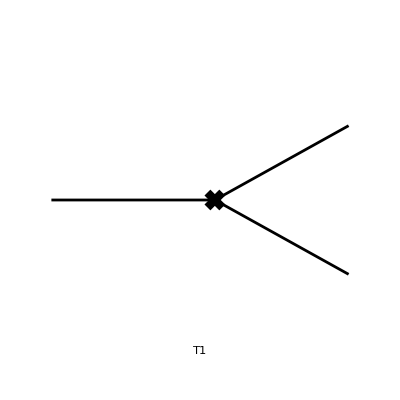

```mathematica
tops1CT=CreateCTTopologies[1,1->2,Adjacencies->3,ExcludeTopologies->{TadpoleCTs,WFCorrectionCTs}];
Paint[tops1CT];
```

## Insertions

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 1 Generic, 1 Classes, 1 Particles insertions

in total: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 1 ad/bdcd/0.m, 0 diagrams

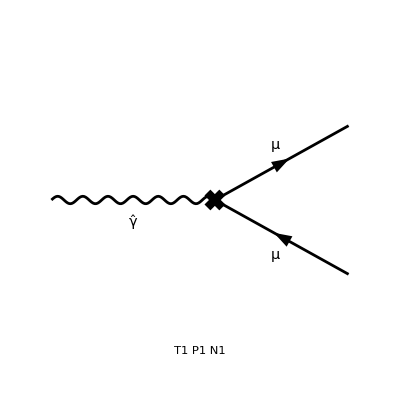

```mathematica
ins1CT=InsertFields[tops1CT, process];
Paint[ins1CT, PaintLevel->{Particles}];
```

## Feynman Amplitudes

```mathematica
ClearProcess[]
```

```mathematica
amp1CT=CalcFeynAmp[CreateFeynAmp[ins1CT,AmplitudeLevel->{Particles}],FermionChains -> Chiral]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

Amp[{{V[10],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-1/2 EL (dZfL1[2,2,2]^*+dZfL1[2,2,2]) Mat[F1]-1/2 EL (dZfR1[2,2,2]^*+dZfR1[2,2,2]) Mat[F2]]

## Squared Matrix Elements

```mathematica
_Hel=0;
```

```mathematica
sm1CT=SquaredME[amp1CT,ampBorn]//Simplify;
sm1CT=sm1CT/.HelicityME[sm1CT];
sm1CT=PolarizationSum[sm1CT]//Simplify
```

> 4 helicity matrix elements

preparing FORM code in /home/riccardo/fc-hel-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-pol-1.frm

running FORM...

ok

2 Alfa MM2 π (dZfL1[2,2,2]^*+dZfR1[2,2,2]^*+dZfL1[2,2,2]+dZfR1[2,2,2])

```mathematica
replaceRC=List@@CalcRenConst[sm1CT][[1]];
```

dZfL1[2,2,2]

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 2: 2 Generic, 6 Classes, 6 Particles insertions

in total: 2 Generic, 6 Classes, 6 Particles insertions

creating amplitudes at level(s) {Generic,Classes,Particles}

> Top. 1: 2 Generic, 6 Classes, 6 Particles amplitudes

in total: 2 Generic, 6 Classes, 6 Particles amplitudes

preparing FORM code in /home/riccardo/fc-rc-1.frm

running FORM...

ok

dZfR1[2,2,2]

```mathematica
sm1CTcomplete=sm1CT//.Subexpr[]//Simplify
```

2 Alfa MM2 π (dZfL1[2,2,2]^*+dZfR1[2,2,2]^*+dZfL1[2,2,2]+dZfR1[2,2,2])

```mathematica
sm1CTL1=sm1CTcomplete//Coefficient[#,dZfL1[2,2,2]]&
sm1CTL1c=sm1CTcomplete//Coefficient[#,Conjugate[dZfL1[2,2,2]]]&
sm1CTR1=sm1CTcomplete//Coefficient[#,dZfR1[2,2,2]]&
sm1CTR1c=sm1CTcomplete//Coefficient[#,Conjugate[dZfR1[2,2,2]]]&
```

2 Alfa MM2 π

2 Alfa MM2 π

2 Alfa MM2 π

«1 more identical outputs»

```mathematica
uvdZL1=UVDivergentPart[dZfL1[2,2,2]/.replaceRC]//Simplify
uvdZL1c=UVDivergentPart[Conjugate[dZfL1[2,2,2]]/.replaceRC]//Simplify
uvdZR1=UVDivergentPart[dZfR1[2,2,2]/.replaceRC]//Simplify
uvdZR1c=UVDivergentPart[Conjugate[dZfR1[2,2,2]]/.replaceRC]//Simplify
```

-(Alfa Divergence (MW2 (1-2 SW2)^2+CW2 (MM2+2 MW2+4 MW2 SW2)))/(16 CW2 MW2 π SW2)

-(Alfa Divergence (MW2 (1-2 SW2)^2+CW2 (MM2+2 MW2+4 MW2 SW2)))/(16 CW2 MW2 π SW2)

-(Alfa Divergence (2 MW2 SW2^2+CW2 (MM2+2 MW2 SW2)))/(8 CW2 MW2 π SW2)

-(Alfa Divergence (2 MW2 SW2^2+CW2 (MM2+2 MW2 SW2)))/(8 CW2 MW2 π SW2)

```mathematica
divergenceCT=sm1CTL1*uvdZL1+sm1CTR1*uvdZR1+Conjugate[sm1CTL1*uvdZL1+sm1CTR1*uvdZR1]//Simplify
```

-(Alfa2 Divergence MM2 (3 CW2 MM2+MW2+2 CW2 MW2-4 MW2 SW2+8 CW2 MW2 SW2+8 MW2 SW2^2))/(4 CW2 MW2 SW2)

```mathematica
uv
```

(Alfa2 Divergence MM2 (3 CW2 MM2+MW2+2 CW2 MW2-4 MW2 SW2+8 CW2 MW2 SW2+8 MW2 SW2^2))/(4 CW2 MW2 SW2)

```mathematica
smBorn
```

8 Alfa MM2 π

```mathematica
cct=divergenceCT/smBorn
```

-(Alfa Divergence (3 CW2 MM2+MW2+2 CW2 MW2-4 MW2 SW2+8 CW2 MW2 SW2+8 MW2 SW2^2))/(32 CW2 MW2 π SW2)

```mathematica
cl=uv/smBorn
```

(Alfa Divergence (3 CW2 MM2+MW2+2 CW2 MW2-4 MW2 SW2+8 CW2 MW2 SW2+8 MW2 SW2^2))/(32 CW2 MW2 π SW2)

```mathematica
cl+cct//Simplify
```

0

## CounterTerms List

## Feynman Amplitudes

```mathematica
ClearProcess[]
```

```mathematica
amp1CTList=calcFeynAmpList[CreateFeynAmp[ins1CT]]
```

creating amplitudes at level(s) {Generic,Classes,Particles}

> Top. 1: 1 Generic, 1 Classes, 1 Particles amplitudes

> Top. 2: 1 Generic, 1 Classes, 1 Particles amplitudes

> Top. 3: 1 Generic, 1 Classes, 1 Particles amplitudes

in total: 3 Generic, 3 Classes, 3 Particles amplitudes

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

{Amp[{{V[2],k[1],MZ,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-(EL Sub27 Mat[F1])/(4 CW SW)-(EL Sub28 Mat[F2])/(2 CW)],Amp[{{V[2],k[1],MZ,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][(EL Sub36 (1-2 SW2) Den[MM2,MM2] Mat[F1])/(4 CW SW)-(EL Sub35 SW Den[MM2,MM2] Mat[F2])/(2 CW)],Amp[{{V[2],k[1],MZ,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][(EL Sub38 (1-2 SW2) Den[MM2,MM2] Mat[F1])/(4 CW SW)-(EL Sub37 SW Den[MM2,MM2] Mat[F2])/(2 CW)]}

## Squared Matrix Elements

```mathematica
_Hel=0;
```

```mathematica
sm1CTList=Map[SquaredME[#,ampBorn]&,amp1CTList]//Simplify;
sm1CTList=Map[(#/.HelicityME[#])&,sm1CTList];
sm1CTList=Map[PolarizationSum[#]&,sm1CTList]//Simplify
```

> 4 helicity matrix elements

preparing FORM code in /home/riccardo/fc-hel-1.frm

running FORM...

ok

> 4 helicity matrix elements

preparing FORM code in /home/riccardo/fc-hel-1.frm

running FORM...

ok

> 4 helicity matrix elements

preparing FORM code in /home/riccardo/fc-hel-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-pol-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-pol-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-pol-1.frm

running FORM...

ok

{1/(4 CW2 SW)Alfa π (2 Sub42 (-3 MM2+4 MM2 SW2+2 MZ2 SW2)+CW Sub40 (MM2-MZ2+4 MM2 SW2+2 MZ2 SW2)+2 CW (2 MZ2 SW2+MM2 (-3+4 SW2)) dZAZ1^*),(Alfa MM π (MZ2 (1-4 SW2+8 SW2^2)+MM2 (-1-8 SW2+16 SW2^2)) dMf1[2,2]^* Den[MM2,MM2])/(CW2 SW2),(Alfa MM π (MZ2 (1-4 SW2+8 SW2^2)+MM2 (-1-8 SW2+16 SW2^2)) dMf1[2,2]^* Den[MM2,MM2])/(CW2 SW2)}

```mathematica
{a,b}=UVDivergentPart[FieldRC[F[2,{2}]]]//FullSimplify
```

{-(Alfa Divergence (MW2+CW2 (MM2+2 MW2)))/(16 CW2 MW2 π SW2),-(Alfa Divergence (2 MW2 SW2^2+CW2 (MM2+2 MW2 SW2)))/(8 CW2 MW2 π SW2)}

```mathematica
smBorn
```

(Alfa π (MZ2 (1-4 SW2+8 SW2^2)+MM2 (-1-8 SW2+16 SW2^2)))/(2 CW2 SW2)

```mathematica
uv=UVDivergentPart[sm1Loop//.Subexpr[]]//Simplify
```

(Alfa2 Divergence (MZ2 (1-4 SW2+8 SW2^2)+MM2 (-1-8 SW2+16 SW2^2)))/(8 CW2 SW2)

```mathematica
uv/smBorn//Simplify
```

(Alfa Divergence)/(4 π)

```mathematica
(a +b)/smBorn//Simplify
```

-(Divergence (MW2+4 MW2 SW2^2+CW2 (3 MM2+2 MW2+4 MW2 SW2)))/(8 MW2 π^2 (MZ2 (1-4 SW2+8 SW2^2)+MM2 (-1-8 SW2+16 SW2^2)))

```mathematica
b/smBorn//Simplify
```

-(Divergence (2 MW2 SW2^2+CW2 (MM2+2 MW2 SW2)))/(4 MW2 π^2 (MZ2 (1-4 SW2+8 SW2^2)+MM2 (-1-8 SW2+16 SW2^2)))

```mathematica
??FieldRC
```

```mathematica
CalcRenConst[dZfL1[2,{2}]]
```

dZfL1[2,2]

{RenConstList[RenConst][dZfL1[2,2]→RenConst[dZfL1[2,2]]]}

```mathematica
df1=dMf1[2,2]/.CalcRenConst[sm1CTList[[2]]][[1,1]]
```

dMf1[2,2]

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 2: 2 Generic, 6 Classes, 6 Particles insertions

in total: 2 Generic, 6 Classes, 6 Particles insertions

creating amplitudes at level(s) {Generic,Classes,Particles}

> Top. 1: 2 Generic, 6 Classes, 6 Particles amplitudes

in total: 2 Generic, 6 Classes, 6 Particles amplitudes

preparing FORM code in /home/riccardo/fc-rc-1.frm

running FORM...

ok

1/π Alfa MM (Finite/(4 CW2)-Re[B0i[bb0,MM2,0,MM2]]+(1/16 MM2 Re[B0i[bb0,MM2,MH2,MM2]]-((CW2 MM2-MW2 (8 SW2-16 SW2^2)) Re[B0i[bb0,MM2,MM2,MZ2]])/(16 CW2))/(MW2 SW2))+MM (-(Alfa Finite)/(8 CW2 π)-(Alfa Finite (1+2 CW2-(4-4 CW2) SW2+4 SW2^2))/(32 CW2 π SW2)-(Alfa (MM2+2 MW2) Re[B0i[bb1,MM2,0,MW2]])/(16 MW2 π SW2)-(Alfa Re[B0i[bb1,MM2,MM2,0]])/(2 π)-(Alfa MM2 Re[B0i[bb1,MM2,MM2,MH2]])/(16 MW2 π SW2)-(Alfa (CW2 MM2+MW2-4 MW2 SW2+8 MW2 SW2^2) Re[B0i[bb1,MM2,MM2,MZ2]])/(16 CW2 MW2 π SW2))

```mathematica
df1//.Subexpr[]//UVDivergentPart//Simplify
```

(Alfa Divergence MM (3 CW2 MM2+MW2+2 CW2 MW2+12 MW2 SW2-24 CW2 MW2 SW2-24 MW2 SW2^2))/(32 CW2 MW2 π SW2)

```mathematica
df2=dMf1[2,2]/.CalcRenConst[sm1CTList[[3]]][[1,1]]
```

dMf1[2,2]

1/π Alfa MM (Finite/(4 CW2)-Re[B0i[bb0,MM2,0,MM2]]+(1/16 MM2 Re[B0i[bb0,MM2,MH2,MM2]]-((CW2 MM2-MW2 (8 SW2-16 SW2^2)) Re[B0i[bb0,MM2,MM2,MZ2]])/(16 CW2))/(MW2 SW2))+MM (-(Alfa Finite)/(8 CW2 π)-(Alfa Finite (1+2 CW2-(4-4 CW2) SW2+4 SW2^2))/(32 CW2 π SW2)-(Alfa (MM2+2 MW2) Re[B0i[bb1,MM2,0,MW2]])/(16 MW2 π SW2)-(Alfa Re[B0i[bb1,MM2,MM2,0]])/(2 π)-(Alfa MM2 Re[B0i[bb1,MM2,MM2,MH2]])/(16 MW2 π SW2)-(Alfa (CW2 MM2+MW2-4 MW2 SW2+8 MW2 SW2^2) Re[B0i[bb1,MM2,MM2,MZ2]])/(16 CW2 MW2 π SW2))

## Results

```mathematica
smBorn
```

8 Alfa MM2 π

```mathematica
sm1Loop
```

-2 Alfa2 MM2 (Sub2+4 MM2 Sub3)

```mathematica
sm1LoopUV=UVDivergentPart[sm1Loop//.Subexpr[]]//Simplify
```

(Alfa2 Divergence (MZ2 (1-4 SW2+8 SW2^2)+MM2 (-1-8 SW2+16 SW2^2)))/(8 CW2 SW2)

```mathematica
sm1CTUVList=Map[UVDivergentPart,sm1CTList]//Simplify
```

{(Alfa CW π (2 MZ2 SW2+MM2 (-3+4 SW2)) dZAZ1^*)/(2 CW2 SW),(Alfa MM π (MZ2 (1-4 SW2+8 SW2^2)+MM2 (-1-8 SW2+16 SW2^2)) dMf1[2,2]^* Den[MM2,MM2])/(CW2 SW2),(Alfa MM π (MZ2 (1-4 SW2+8 SW2^2)+MM2 (-1-8 SW2+16 SW2^2)) dMf1[2,2]^* Den[MM2,MM2])/(CW2 SW2)}

```mathematica
UVDivergentPart[df1]+UVDivergentPart[df2]//Simplify
```

(Alfa Divergence MM (3 CW2 MM2+MW2+2 CW2 MW2+12 MW2 SW2-24 CW2 MW2 SW2-24 MW2 SW2^2))/(16 CW2 MW2 π SW2)

## One-Loop - Z Boson

## Insertions

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 6 Generic, 14 Classes, 14 Particles insertions

in total: 6 Generic, 14 Classes, 14 Particles insertions

> Top. 1 ad/becf/dedfef.m, 0 diagrams

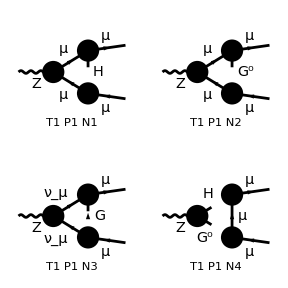

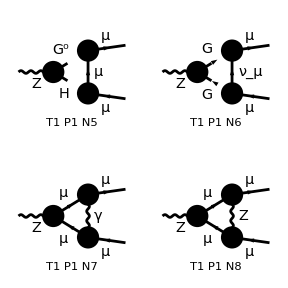

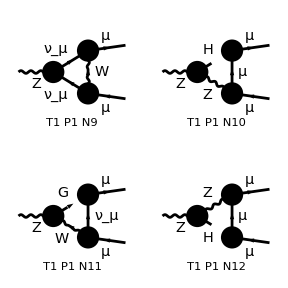

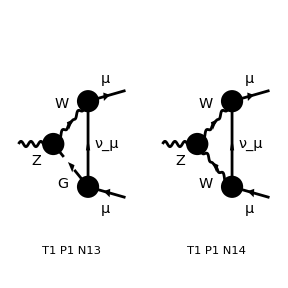

```mathematica
ins1LoopZ=InsertFields[tops1Loop, process];
ins1LoopZ=DiagramSelect[ins1LoopZ, !FreeQ[#,V[2]]&];
Paint[ins1LoopZ, PaintLevel->{Particles}];
```

## Feynman Amplitudes

```mathematica
ClearProcess[]
```

```mathematica
amp1LoopZ=CalcFeynAmp[CreateFeynAmp[ins1LoopZ,AmplitudeLevel->{Particles}],FermionChains -> Chiral]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 14 Particles amplitudes

in total: 14 Particles amplitudes

preparing FORM code in /home/riccardo/fc-amp-6.frm

running FORM...

ok

Amp[{{V[2],k[1],MZ,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][1/π Alfa EL MM Pair1 (1/SW(1/(CW MW2)MM2 (-((1-2 SW2) C0i[cc1,MM2,MZ2,MM2,MH2,MM2,MM2])/(8 SW2)+1/16 (-Sub211 C0i[cc1,MZ2,MM2,MM2,MM2,MM2,MZ2]-Sub111 C0i[cc12,MM2,MZ2,MM2,MH2,MM2,MM2]))+(CW C0i[cc22,MM2,MZ2,MM2,0,MW2,MW2])/(2 SW2)+1/8 (Sub411 C0i[cc1,MM2,MZ2,MM2,0,MW2,MW2]+(Sub271 C0i[cc12,MM2,MZ2,MM2,0,MW2,MW2])/SW2+(MM2 (C0i[cc22,MM2,MZ2,MM2,MH2,MM2,MM2]+C0i[cc22,MZ2,MM2,MM2,0,0,MW2]/SW2))/(CW MW2)))+1/CW(SW (C0i[cc1,MM2,MZ2,MM2,0,MM2,MM2]+C0i[cc11,MM2,MZ2,MM2,0,MM2,MM2])+1/2 Sub1 C0i[cc12,MM2,MZ2,MM2,0,MM2,MM2]+1/SW((Sub111 C0i[cc2,MM2,MM2,MZ2,MH2,MM2,MZ2])/(8 CW2)+1/MW2 MM2 (1/SW2(1/8 (CW2-SW2) C0i[cc11,MM2,MZ2,MM2,0,MW2,MW2]-1/16 (1-2 SW2) (C0i[cc0,MZ2,MM2,MM2,MM2,MM2,MZ2]+C0i[cc11,MM2,MZ2,MM2,MH2,MM2,MM2]))+1/4 C0i[cc2,MM2,MZ2,MM2,MH2,MM2,MM2])-((2-MM2/MW2) (C0i[cc12,MZ2,MM2,MM2,0,0,MW2]+C0i[cc2,MZ2,MM2,MM2,0,0,MW2]))/(8 SW2))+(1-2 SW2) (-1/8 Sub112 C0i[cc2,MZ2,MM2,MM2,MM2,MM2,MZ2]-(C0i[cc2,MM2,MZ2,MM2,0,MM2,MM2]+C0i[cc22,MM2,MZ2,MM2,0,MM2,MM2])/(2 SW))+1/16 (Sub231 C0i[cc12,MZ2,MM2,MM2,MM2,MM2,MZ2]+Sub241 C0i[cc22,MZ2,MM2,MM2,MM2,MM2,MZ2]))) Mat[F1]+1/π Alfa EL (1/SW((Finite Sub71)/32+1/SW2(1/8 (-(1/CW-2 CW) B0i[bb0,MM2,0,MW2]-(MM2^2 (1-2 SW2) C0i[cc0,MM2,MZ2,MM2,MH2,MM2,MM2])/(CW MW2))+CW (-1/4 (MM2-MW2) C0i[cc0,MM2,MZ2,MM2,0,MW2,MW2]+1/2 C0i[cc00,MM2,MZ2,MM2,0,MW2,MW2]))+1/8 Sub291 C0i[cc1,MM2,MZ2,MM2,0,MW2,MW2]+1/CW(1/16 (-(MM2 B0i[bb0,MM2,MH2,MM2])/MW2-Sub151 B0i[bb0,MM2,MM2,MZ2])+(1-2 SW2) (1/4 (B0i[bb0,MM2,0,MM2]+(2 MM2-MZ2) C0i[cc0,MM2,MZ2,MM2,0,MM2,MM2])-1/2 C0i[cc00,MM2,MZ2,MM2,0,MM2,MM2]+1/(CW2 SW2)MM2 (-1/4 C0i[cc0,MM2,MM2,MZ2,MH2,MM2,MZ2]-1/8 C0i[cc1,MM2,MM2,MZ2,MH2,MM2,MZ2]))+1/SW2(1/4 C0i[cc00,MZ2,MM2,MM2,0,0,MW2]-(MM2^2 (1-2 SW2) C0i[cc1,MM2,MZ2,MM2,MH2,MM2,MM2])/(16 MW2)-1/8 MZ2 C0i[cc1,MZ2,MM2,MM2,0,0,MW2])+Sub151 (1/8 C0i[cc00,MZ2,MM2,MM2,MM2,MM2,MZ2]-1/16 MZ2 C0i[cc1,MZ2,MM2,MM2,MM2,MM2,MZ2])+MM2 (-1/16 Sub91 C0i[cc0,MZ2,MM2,MM2,MM2,MM2,MZ2]+(C0i[cc00,MM2,MM2,MZ2,MH2,MM2,MZ2]/SW2+C0i[cc00,MM2,MZ2,MM2,MH2,MM2,MM2])/(8 MW2)-(Sub111 C0i[cc2,MM2,MM2,MZ2,MH2,MM2,MZ2])/(8 CW2))))+MM2 (-(Sub1 C0i[cc2,MM2,MZ2,MM2,0,MM2,MM2])/(4 CW)+(1/8 (1/CW+CW/SW2) C0i[cc2,MM2,MZ2,MM2,0,MW2,MW2]-(Sub141 C0i[cc2,MM2,MZ2,MM2,MH2,MM2,MM2])/(16 CW MW2))/SW)+1/CW(-1/4 Sub3 C0i[cc1,MM2,MZ2,MM2,0,MM2,MM2]+1/16 (-(Sub161 C0i[cc2,MZ2,MM2,MM2,0,0,MW2])/(SW SW2)-Sub191 C0i[cc2,MZ2,MM2,MM2,MM2,MM2,MZ2]))) Mat[F2]+1/π Alfa EL MM Pair1 (1/SW(1/CW(-1/2 (1-2 SW2) (C0i[cc1,MM2,MZ2,MM2,0,MM2,MM2]+C0i[cc11,MM2,MZ2,MM2,0,MM2,MM2])+1/MW2 MM2 (1/4 C0i[cc1,MM2,MZ2,MM2,MH2,MM2,MM2]+1/16 Sub211 C0i[cc1,MZ2,MM2,MM2,MM2,MM2,MZ2]+1/8 (C0i[cc0,MZ2,MM2,MM2,MM2,MM2,MZ2]+C0i[cc11,MM2,MZ2,MM2,MH2,MM2,MM2])-1/16 Sub111 C0i[cc12,MM2,MZ2,MM2,MH2,MM2,MM2])+((2-MM2/MW2) C0i[cc12,MZ2,MM2,MM2,0,0,MW2])/(8 SW2))+1/8 Sub411 C0i[cc2,MM2,MZ2,MM2,0,MW2,MW2]+1/SW2(1/2 CW C0i[cc11,MM2,MZ2,MM2,0,MW2,MW2]+1/8 Sub271 C0i[cc12,MM2,MZ2,MM2,0,MW2,MW2]-(MM2 (1-2 SW2) C0i[cc2,MM2,MZ2,MM2,MH2,MM2,MM2])/(8 CW MW2)))+1/CW(1/2 Sub1 C0i[cc12,MM2,MZ2,MM2,0,MM2,MM2]-1/16 Sub231 C0i[cc12,MZ2,MM2,MM2,MM2,MM2,MZ2]+1/4 Sub131 C0i[cc2,MZ2,MM2,MM2,MM2,MM2,MZ2]+SW (C0i[cc2,MM2,MZ2,MM2,0,MM2,MM2]+C0i[cc22,MM2,MZ2,MM2,0,MM2,MM2])+1/SW(1/SW2(1/MW2 MM2 (1/8 (CW2-SW2) C0i[cc22,MM2,MZ2,MM2,0,MW2,MW2]-1/16 (1-2 SW2) C0i[cc22,MM2,MZ2,MM2,MH2,MM2,MM2])+1/4 C0i[cc22,MZ2,MM2,MM2,0,0,MW2])+1/8 ((Sub111 C0i[cc2,MM2,MM2,MZ2,MH2,MM2,MZ2])/CW2+Sub151 C0i[cc22,MZ2,MM2,MM2,MM2,MM2,MZ2])))) Mat[F3]+1/π Alfa EL (1/SW MM2 (-1/8 (1/CW-(3 CW)/SW2) (C0i[cc1,MM2,MZ2,MM2,0,MW2,MW2]+C0i[cc2,MM2,MZ2,MM2,0,MW2,MW2])+(Sub171 C0i[cc2,MM2,MZ2,MM2,MH2,MM2,MM2])/(32 CW MW2))+1/CW(SW (1/4 Finite (1+SW2/CW2)+1/2 (-B0i[bb0,MM2,0,MM2]-(2 MM2-MZ2) C0i[cc0,MM2,MZ2,MM2,0,MM2,MM2])+C0i[cc00,MM2,MZ2,MM2,0,MM2,MM2])+1/4 ((MM2 C0i[cc1,MM2,MM2,MZ2,MH2,MM2,MZ2])/(CW2 SW)+Sub4 C0i[cc1,MM2,MZ2,MM2,0,MM2,MM2])+Sub241 (1/16 C0i[cc00,MZ2,MM2,MM2,MM2,MM2,MZ2]+1/32 (-B0i[bb0,MM2,MM2,MZ2]-MZ2 C0i[cc1,MZ2,MM2,MM2,MM2,MM2,MZ2]))+MM2 (-1/16 Sub212 C0i[cc0,MZ2,MM2,MM2,MM2,MM2,MZ2]+1/SW(1/(MW2 SW2)(-1/16 B0i[bb0,MM2,0,MW2]+1/32 (1-2 SW2) B0i[bb0,MM2,MH2,MM2]-1/8 C0i[cc00,MM2,MM2,MZ2,MH2,MM2,MZ2])+1/CW2(1/2 C0i[cc0,MM2,MM2,MZ2,MH2,MM2,MZ2]-1/8 Sub111 C0i[cc2,MM2,MM2,MZ2,MH2,MM2,MZ2]))-1/4 Sub1 C0i[cc2,MM2,MZ2,MM2,0,MM2,MM2])+1/SW(1/MW2(MM2^2 (1/4 C0i[cc0,MM2,MZ2,MM2,MH2,MM2,MM2]+1/8 C0i[cc1,MM2,MZ2,MM2,MH2,MM2,MM2])+1/SW2 MM2 (1/8 ((CW2-SW2) C0i[cc00,MM2,MZ2,MM2,0,MW2,MW2]+C0i[cc00,MZ2,MM2,MM2,0,0,MW2])+1/16 (-(1-2 SW2) C0i[cc00,MM2,MZ2,MM2,MH2,MM2,MM2]-MZ2 C0i[cc1,MZ2,MM2,MM2,0,0,MW2])))-(Sub281 C0i[cc2,MZ2,MM2,MM2,0,0,MW2])/(16 SW2))+1/16 Sub261 C0i[cc2,MZ2,MM2,MM2,MM2,MM2,MZ2])) Mat[F4]]

## Squared Matrix Elements

```mathematica
_Hel=0;
```

```mathematica
sm1LoopZ=SquaredME[amp1LoopZ,ampBorn]//Simplify;
sm1LoopZ=sm1LoopZ/.HelicityME[sm1LoopZ];
sm1LoopZ=PolarizationSum[sm1LoopZ]//Simplify
```

> 16 helicity matrix elements

preparing FORM code in /home/riccardo/fc-hel-6.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-pol-7.frm

running FORM...

ok

1/(64 CW CW2 SW)Alfa2 (2 CW Sub1111 (2 MZ2 SW2+MM2 (-3+4 SW2))-CW2 (2 MZ2 Sub711 (-1+2 SW2)+4 MM2^2 (Sub50+Sub87) (-1+4 SW2)-MM2 MZ2 (Sub50+Sub87) (-1+4 SW2)+2 MM2 Sub711 (1+4 SW2)))

```mathematica
UVDivergentPart[sm1LoopZ]
```

0

## One-Loop - W Boson

## Insertions

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 6 Generic, 14 Classes, 14 Particles insertions

in total: 6 Generic, 14 Classes, 14 Particles insertions

> Top. 1 ad/becf/dedfef.m, 0 diagrams

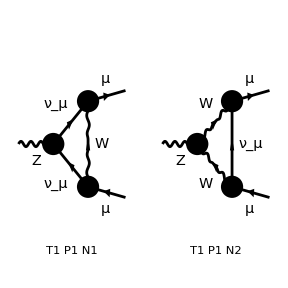

```mathematica
ins1LoopW=InsertFields[tops1Loop, process];
ins1LoopW=DiagramSelect[ins1LoopW,!FreeQ[#,V[3]]&& FreeQ[#,S]&];
Paint[ins1LoopW, PaintLevel->{Particles}];
```

## Feynman Amplitudes

```mathematica
ClearProcess[]
```

```mathematica
amp1LoopW=CalcFeynAmp[CreateFeynAmp[ins1LoopW,AmplitudeLevel->{Particles}],FermionChains -> Chiral];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

preparing FORM code in /home/riccardo/fc-amp-7.frm

running FORM...

ok

```mathematica
amp1LoopWList=Map[CalcFeynAmp[CreateFeynAmp[ins1LoopW[[0]][#],AmplitudeLevel->{Particles}],FermionChains -> Chiral]&,ins1LoopW];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

preparing FORM code in /home/riccardo/fc-amp-7.frm

running FORM...

ok

## Squared Matrix Elements

```mathematica
_Hel=0;
```

```mathematica
sm1LoopW=SquaredME[amp1LoopW,ampBorn]//Simplify;
sm1LoopW=sm1LoopW/.HelicityME[sm1LoopW];
sm1LoopW=PolarizationSum[sm1LoopW]//Simplify
```

> 16 helicity matrix elements

preparing FORM code in /home/riccardo/fc-hel-7.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-pol-7.frm

running FORM...

ok

-1/(16 CW2 SW2^2)Alfa2 (MZ2 Sub118 (-1+2 SW2)+2 MM2^2 (-2 Sub1211-3 Sub123+Sub115 (2-8 SW2)+8 Sub1211 SW2+4 Sub123 SW2)+MM2 (Sub118+4 Sub118 SW2+MZ2 (-Sub115+Sub1211+4 Sub115 SW2-4 Sub1211 SW2+4 Sub123 SW2)))

```mathematica
UVDivergentPart[sm1LoopW]
```

0